```mathematica
Clear["Global`*"]
tp:=0.4; d1:=0.12; d2:=0.12;  c:=6.25;
A1[U_]:=U^2+(d1^2+d2^2)/2+tp^2/2;
A3[U_]:=U^4-U^2*(d1^2+d2^2)+d1^2*d2^2+tp^2*(U^2-U*(d1+d2)+d1*d2);
A7[U_]:=2*U^2-d1^2-d2^2;
a[x_,U_]:=2*((c*x)^2+A1[U]);
b[U_]:=2*(U*(d1^2-d2^2)+tp^2*(d1-d2)/2);
ch[x_,U_]:=4*(A3[U]-A7[U]*(c*x)^2+(c*x)^4);
dh[x_,U_]:=a[x,U]*ch[x,U]+b[U]^2;
s[x_,U_]:=-a[x,U]^2/3-ch[x,U];
qh[x_,U_]:=(2*a[x,U]^3/27+(a[x,U]*ch[x,U])/3-dh[x,U]);
Q1[x_,U_]:=((qh[x,U]^2)/4+(s[x,U]^3)/27);
Q[x_,U_]:=Sqrt[Q1[x,U]];
Y[x_,U_]:=(-qh[x,U]/2+Q[x,U])^(1/3)+(-qh[x,U]/2-Q[x,U])^(1/3);
r[x_,U_]:=Y[x,U]-a[x,U]/3;
f[x_,U_]:=Sqrt[(r[x,U]+a[x,U])];  
g[x_,U_]:=(b[U]+r[x,U]*f[x,U])/(2*f[x,U]);
G[x_,U_]:=(b[U]-r[x,U]*f[x,U])/(2*f[x,U]);
f1[x_,U_]:=(-f[x,U]+(f[x,U]^2-4*g[x,U])^(1/2))/2;  
f2[x_,U_]:=(-f[x,U]-(f[x,U]^2-4*g[x,U])^(1/2))/2;
f3[x_,U_]:=(f[x,U]+(f[x,U]^2+4*G[x,U])^(1/2))/2;
 f4[x_,U_]:=(f[x,U]-(f[x,U]^2+4*G[x,U])^(1/2))/2;   
v1[x_]=tp/2+Sqrt[(c*x)^2+(tp/2+d1)^2];
v2[x_]=tp/2-Sqrt[(c*x)^2+(tp/2+d1)^2];
v3[x_]=-tp/2+Sqrt[(c*x)^2+(tp/2-d1)^2];
v4[x_]=-tp/2-Sqrt[(c*x)^2+(tp/2-d1)^2];
```

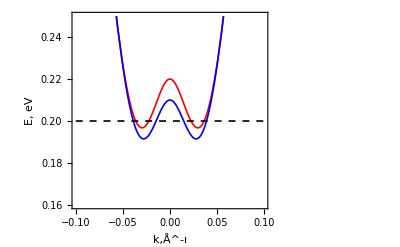

```mathematica
Plot[{f4[x,-0.1],f4[x,-0.09],0.2},{x,-0.1,0.1},Epilog->{{Black,Text["Δ_2= 100 meV",{0.14,0.25},{-1,-1}]},{Black,Text["Δ_2=-100 meV",{0.14,0.15},{-1,-1}]}},PlotStyle->{{Thickness[0.003],Red},{Thickness[0.003],Blue},{Thickness[0.003],Dashed,Black}},FrameLabel->{"k,Å^-ı","E, eV"},PlotRange->{0.16,0.25},Frame->True]
```

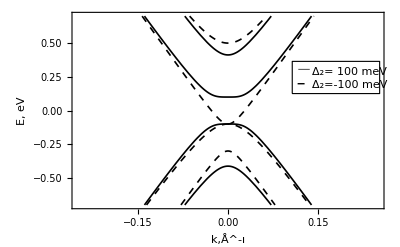

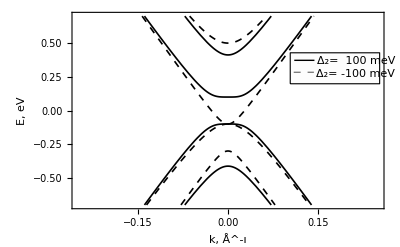

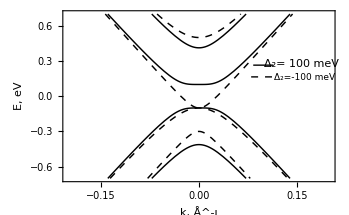

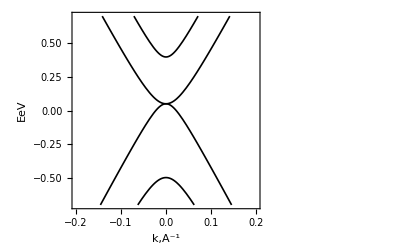

```mathematica
d1:=0.05
data1=Table[{α,NMinimize[Re[f4[x,α]-f1[x,α]],x][[1]]},{α,-0.25,0.25,0.01}];
d1:=-0.05
data2=Table[{α,NMinimize[Re[f4[x,α]-f1[x,α]],x][[1]]},{α,-0.25,0.25,0.01}];
```

```mathematica
ListPlot[{data1,data2},Joined->True,PlotStyle-> {{Thickness[0.003],Red},{Thickness[0.003],Blue}},PlotRange->{0,0.5},FrameLabel->{"U, eV","Δ, eV"},Frame->True]
```

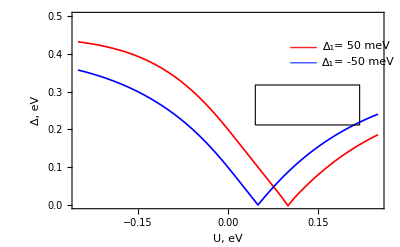

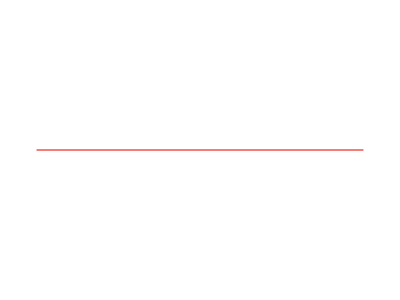

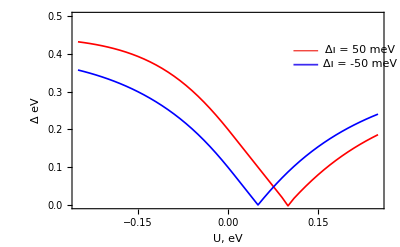

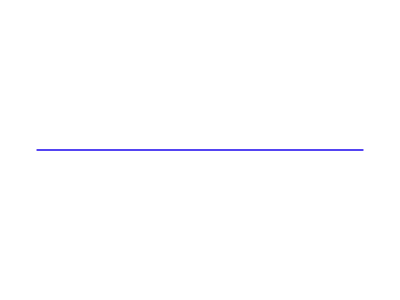

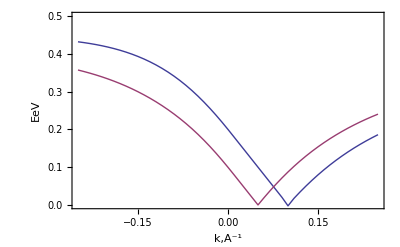

```mathematica
Export["A16.pdf",ListPlot[{data1,data2},Joined->True,PlotRange->{0,0.5},AxesLabel->{"k,A^-1",EeV},Frame->True]]
```

A16.pdf